# M1: The Simple Pendulum

## Priyanka Makin Maya Fabrikant 09/29/2016

## Introduction

In this lab we explored simple harmonic motion using a pendulum. We first computed the acceleration of gravity by making initial measurements of the length of our pendulum and its period.We then varied the length of the pendulum and its amplitude and analyzed the effect it had on the pendulum’s period for a swing.

## Part 1: Precision Determination of g

```mathematica
h = 0.034; (*Height of the Mass in m*)
δh = 0.001; (*Uncertainty in m*)

λ = 1.235; (*Length of the string in m*)
δλ  = 0.001; (*Uncertainty in m*)

L = λ+(1/2)h; (*Length of the Pendulum in m*)
δL = √(δh^2+δh^2); (*Uncertainty of the length*)

Tper = 2.2407; (*Period of 1 oscillation in s*)
δTper = 0.0002; (*Uncertainty in s*)

gknown = 9.769; (*Known value of g in m/s^2*)
gmeas = 4 π^2*L/Tper^2 (*Calculating our measured value of g*)
δmeas = gmeas √((δL/L)^2+2(δTper/Tper)^2) (*Uncertainty of measured g*)
Δgmeas = Abs[gmeas - gknown] (*Discrepancy between actual g and measured g*)
```

9.84457

0.0111893

0.0755674

So the measured value of g is (9.84 ± 0.01) m/s^2 with a discrepancy of 0.076  m/s^2.

## Part 2: Dependence of T on L

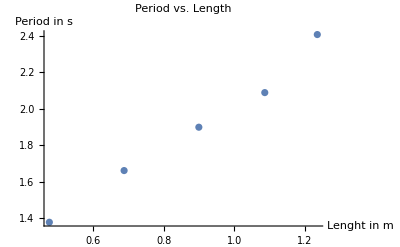

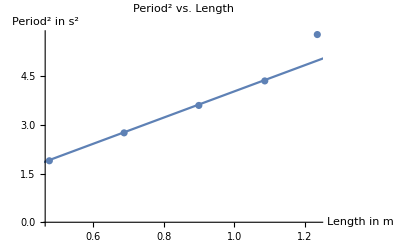

```mathematica
Lengths = {0.475, 0.687, 0.899, 1.086, 1.235}; (*Lengths of different strings in m*)
Per = {1.3775, 1.6610, 1.8988, 2.0886, 2.407}; (*Period of different lengths in s*)
PerSq = Per^2; (*Period square in s^2*)

TvsLData = Thread[{Lengths, Per}];
TvsPerSqData = Thread[{Lengths, PerSq}];

ListPlot[TvsLData, PlotLabel->"Period vs. Length", AxesLabel->{"Lenght in m", "Period in s"}]

Show[ListPlot[TvsPerSqData], Plot[(4 π^2/gknown)x, {x, 0, 1.3}], PlotLabel->"Period^2 vs. Length", AxesLabel->{"Length in m", "Period^2 in s^2"}]
```

When we look at the Period vs. Length graph, it is not obvious if anything is wrong with our data, it’s just a collection of points. But when we analyze the Period^2 vs. Length graph, we can see something strange going on with our data. The first four points seem to sit on the line y(x) = (4π ^(2)x)/g really well, but the last data point is way off.

## Part 3: Dependence of T on Amplitude

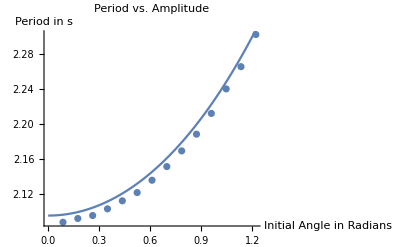

```mathematica
AngleDeg = {5, 10, 15, 20, 25, 30, 35, 40, 45, 50, 55, 60, 65, 70}; (*Amplitude in degrees*)
TAngle = {2.0873, 2.0916, 2.0950, 2.1026, 2.1118, 2.1212, 2.1353, 2.1509, 2.1688, 2.1879, 2.2116, 2.2396, 2.2650, 2.3017}; (*Period of oscillation in s*)

AngleRad = AngleDeg*(π/180);
TvsAData = Thread[{AngleRad, TAngle}];
Show[ListPlot[TvsAData], Plot[2π √(1.086/gknown)(1+(1/16)q^2+(11/3072)q^4), {q, 0, 1.4}], PlotLabel->"Period vs. Amplitude", AxesLabel->{"Initial Angle in Radians", "Period in s"}]
```

This graph looks pretty good. The points do follow the curve of the period equation quite closely. However, none of the points actually lie on it. Our data points seem to be uniformly shifted just a little below the curve. The point with the greatest amplitude is the closest to this curve. It seems as if as the amplitude increased, our measured period got closer to the calculated period.

## Conclusion

If we look back at part 1 of this lab, our measurements seem pretty accurate; we got a relatively close calculation for the acceleration of gravity to the actual measured value. Then, in part 2, we seem to have some discrepancies in our measurements. Our Period vs. Length graph doesn’t seem to be curving the right way (shaped like a x^(1/2) graph), so when we plotted our Period^(2) vs. Length graph it wasn’t completely linear. Then in part 3, our measurements of the period as a whole seem pretty consistent, however they are consistently off of the the calculated periods they should be. In this lab, there were all kinds of opportunities for error. We could have measured the strings inaccurately, not dropped the pendulum consistently, not measured the amplitude accurately, or reported the wrong photogate data. With all this taken into consideration though, I think the lab went pretty well and the measurements we took were quite accurate.